```mathematica
Exit[]
```

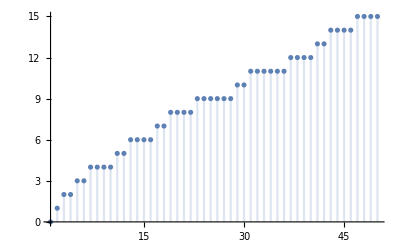

```mathematica
DiscretePlot[PrimePi[k], {k, 1, 50}]
```

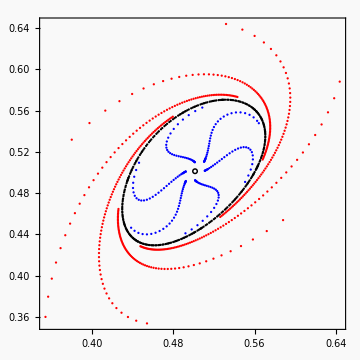

```mathematica
With[{a = 2005/1000, icv = {{0.35, 0.5}, {0.36, 0.51}, {0.51, 0.51}}, 
niterates = {{n, 3000, 5000}, {n, 1, 480}, {n, 1, 1200}}, points = {300, 450, 200},
orbitstyle = {{Black, PointSize[0.0045]}, {Red, 
PointSize[0.0045]}, {Blue, PointSize[0.0045]}}},

fp = Part[{x, y} /. 
NSolve[{a x (1 - y) - x, x - y} == {0, 0} && x > 0 && y > 0, {x, y}], 1]; 


Show@Table[
ListPlot[
RecurrenceTable[{x[n + 1] == a x[n] (1 - y[n]), y[n + 1] == x[n], 
{x[0], y[0]} == {Part[icv[[i]], 1], Part[icv[[i]], 2]}}, {x, y}, niterates[[i]]], 
PlotRange -> All, MaxPlotPoints -> points[[i]], Axes -> False, 
PlotStyle -> orbitstyle[[i]], AspectRatio -> 1, Frame -> True, 
LabelStyle -> Directive[Black, Tiny], 
FrameStyle -> Directive[Black], 
Epilog -> {{PointSize[0.012], Black, 
Point[fp]}, {PointSize[0.006], White, Point[fp]}}, 
Background -> Lighter[Gray, 0.95], ImageSize -> Medium], {i, 1, Length[icv]}]]
```

{{a[n]→-1+2^n+2^(-1+n) C[1]}}

1

{(0.5-0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5+0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n),(0.5+0.5 ⅈ) ⅇ^((0.0000124998-0.100166 ⅈ) n)+(0.5-0.5 ⅈ) ⅇ^((0.0000124998+0.100166 ⅈ) n)}

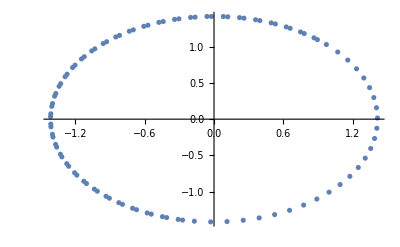

```mathematica
eq1:={Subscript[x, 1][n + 1]- 0.995 Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0}
eq2:={Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - 0.995 Subscript[x, 2][n] == 0}

sys:={Subscript[x, 1][n + 1]- 0.995 Subscript[x, 1][n] + 0.1 Subscript[x, 2][n] == 0, Subscript[x, 2][n + 1]- 0.1 Subscript[x, 1][n] - 0.995 Subscript[x, 2][n] == 0,Subscript[x, 1][0]==Subscript[x, 10],Subscript[x, 2][0]==Subscript[x, 20]}

RSolve[a[n + 1] - 2 a[n] == 1, a[n], n]

Subscript[x, 10]=1;Subscript[x, 20]=1

sol=RSolveValue[sys, {Subscript[x, 1][n],Subscript[x, 2][n]}, {n}]//Simplify

x1sol[n_]:=(0.5-0.5 ⅈ) ⅇ^((0.000012499843752955542-0.10016616488792511 ⅈ) n)+(0.5+0.5 ⅈ) ⅇ^((0.000012499843752955542+0.10016616488792511 ⅈ) n)
x2sol[n_]:=(0.5+0.5 ⅈ) ⅇ^((0.000012499843752955542-0.10016616488792511 ⅈ) n)+(0.5-0.5 ⅈ) ⅇ^((0.000012499843752955542+0.10016616488792511 ⅈ) n)


x1list = Table[x1sol[i], {i, 50}];
x2list = Table[x2sol[i], {i, 50}];


ListPlot[Table[{x1sol[i], x2sol[i]}, {i, 100}]]
```

```mathematica
eq3:={y''[t]==y'[t]  0.001 √((x'[t])^2+(y'[t])^2),x''[t]==-1-0.001x'[t]  √((x'[t])^2+(y'[t])^2),x[0]==0,y[0]==0,x'[0]==1,y'[0]==1}
NDSolve[eq3,{x[t],y[t]},{t,0,2}]

DiscretePlot[Subscript[x, 1][n], {n, 0, 7}]

masterlist = Thread[x1list,x2list]

ListPlot[Thread[{x1list, x2list}]]
ListPlot[masterlist]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}